```mathematica
ClearAll[U,rho1,k,rho]
```

```mathematica
U[r_,a_,b_,n_,u0_] := u0/((2/b*(r-a))^(2*n)+1)
```

```mathematica
rho1[kt_,rs_,a_,b_,n_,u0_,x_?NumericQ] :=rho1[kt,rs,a,b,n,u0,x] = Exp[-U[x,a,b,n,u0]/kt]* NIntegrate[Exp[U[r,a,b,n,u0]/kt]/r^2, {r,rs,x}]
```

```mathematica
rho1[1,1,2,1,10,1,4]
```

1.19841

```mathematica
k[np_,d_,kt_,rs_, rd_ ,a_,b_,n_,u0_] :=k[np,d,kt,rs,rd,a,b,n,u0] = np*d*(NIntegrate[rho1[kt,rs,a,b,n,u0,x],{x,rs,rd}])^(-1)
```

```mathematica
k[1000,0.05,1,1,10,2,1,10,1]
```

5.0838

```mathematica
rho[np_,d_,kt_,rs_,rd_,a_,b_,n_,u0_,r_?NumericQ] := rho[np,d,kt,rs,rd,a,b,n,u0,r] = k[np,d,kt,rs, rd,a,b,n,u0] /(4*Pi*d)*Exp[-U[r,a,b,n,u0]/kt]*NIntegrate[Exp[U[x,a,b,n,u0]/kt]/x^2, {x,rs,r}]
```

```mathematica
np = 100
d = 0.05
kt = 1
rs = 1
rd = 10
a = 4
b = 1
n = 10
u0 = 0
u1 = 1
```

100

0.05

1

1

10

4

1

10

0

1

```mathematica
100
```

100

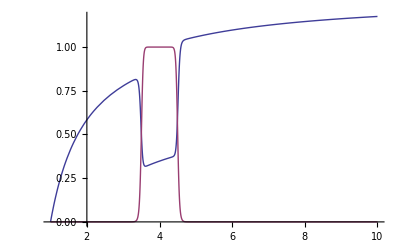

```mathematica
Plot[{rho[np,d,kt,rs,rd,a,b,n,u1,r],U[r,a,b,n,u1]},{r,1,10}]
```

```mathematica
Parallelize[Do[Export[ "/users/stud/jkolb/Veranstaltungen/MA/rateplot" <> ToString[a-rs - (b/2.0)] <>".dat",Table[{y,k[np,d,kt,rs,rd,a,b,n,(u0+y)/2],(k[np/2,d,kt,rs,rd,a,b,n,u0]+k[np/2,d,kt,rs,rd,a,b,n,y] ),k[np,d,kt,rs,rd,a,b,n,(u0+y)/2]-(k[np/2,d,kt,rs,rd,a,b,n,u0]+k[np/2,d,kt,rs,rd,a,b,n,y] )},{y,-10,10,0.1}]],{a,1.5,7,0.5}]]
```